# Hut 1981 tidal evolution

## 1. Recap on Hut 1980

In Hut1980 they minimize total energy, with the constraint of angular momentum conservation. The only parameters are a, e, i, and angular velocities of rotation of both stars, Ω and ω. 

Figure 4 is a bifurcation diagram of the solutions, with orbital velocity vs total angular momentum. Conservation of angular momentum tells us that 

L = h + I_1 Ω+I_2ω

where h is the orbital angular momentum ~ a^(1/2). Our solutions will lie on lines of constant L because of conservation.

The result is that there is a minimum total angular momentum where any (stable) equilibrium solution exists. If the orbital angular momentum constitutes more than 3/4 of this (wide orbit + slow spins), then the system will always move toward a stable equilibrium of circularity, coplanarity and spin-orbit synchronisation (left branch in Fig 4). If the orbital angular momentum is less than 3/4 of the total (tighter orbits + faster spins), an unstable equilibrium exists (right branch in Fig 4). Any deviation to the left flows to the stable solution (binary gets wider, spins slow down until circular, synchronous and coplanar) which will be at some separation a_0 with spins Ω_0 and ω_0. Any deviation to the right is unstable, where the solution flows to merger (binary gets tighter, spins increase)

## 2. Weak friction model (with appendix A)

Structure of paper:
- Assume a constant time lag (in co-rotating frame)
- Derive the perturbing tidal forces
- Derive rates of change of orbital parameters by orbit-averaging the perturbing force.
-Linearize the coupled rate equations, analyze equilibrium solutions
- Get timescales for eccentricity, semi-major axis, rotational velocity and inclination to relax close to equilibrium
-Far from equilibrium (in Hut1980) analyze the global behaviour of the system

We define the ratio of orbital AM to rotational AM:
α = h/(I Ω_0)= q/(1+q)1/r_g^2(a_0/R)^2
Which is the parameter we tweak when looking at stability in Hut1980.

### Glossary

Love number/ apsidal motion constant (k) : between 0 and 1. how centrally condensed is the star? The less centrally condensed, the larger k. As in, it’s easier to deform.
radius of gyration: (M(r_g R))^2=I

small radius of gyration means more centrally condensed (smaller love number) and less angular momentum in spin for the same mass.

### Equipotential surfaces with bulge

We want to plot the gravitational potential , altered by the bulges, seen by a test particle. So we have that
U_total= U_(point mass)+ U_(bulge 1)+ U_(bulge 2)
Let’s forget constants m, G in the problem.

```mathematica
R = 0.8;
k = 0.01
μ[x_,y_]:= 1/2 k (R/((x^2+y^2)^(1/2)))^3
```

0.01

```mathematica
U[θ_][x_,y_]:=(1-2 μ[x,y])/((x^2+y^2)^(1/2))+ μ[x,y]/(((x-R Cos[θ])^2+(y-R Sin[θ])^2)^(1/2))+μ[x,y]/(((x+R Cos[θ])^2+(y+R Sin[θ])^2)^(1/2));
```

```mathematica
cp[θ_]:=ContourPlot[U[θ][x,y],{x,-1.2,1.2},{y,-1.2,1.2},PlotRange->{0,7},FrameLabel->{"x","y"},Contours->Range[0,7,.05],ImageSize->Medium,ColorFunction-> "Rainbow",Axes->True,PlotLegends->Automatic,Epilog->{White,Point[{{R Cos[θ],R Sin[θ]},{0,0},{-R Cos[θ],-R Sin[θ]}}]}]
```

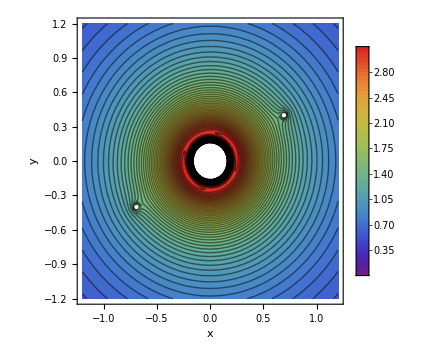

```mathematica
cp[30°]
```

## 3. Local behaviour near equilibria

In this section, we do a local stability analysis around equilibria 

We let the equilibrium values equal a_0, Ω_0 (the equations 15 and 16 are the change of variables required to do linear stability analysis around an origin)

We have also changed the time variable to the ``slow time’’ defined by equation 23. This time depends on the R/a ratio to the power of 8, and also the apsidal motion constant. Keep this in mind when we derive the timescales later.

For stability,  all eigenvalues need to be negative.
We have a set of four coupled linear DEs. We should be able to use some eigenvalue decomposition for our solutions. Let' s try examine the solutions of Eq. 34

```mathematica
MatrixForm[A=3/2 {{6,-38,4,0},{0,-14,0,0},{-3α,12α,-2α,0},{0,0,0,-(1+α)}}]
```

(9 | -57 | 6 | 0
0 | -21 | 0 | 0
-(9 α)/2 | 18 α | -3 α | 0
0 | 0 | 0 | 3/2 (-1-α))

```mathematica
det = Det[A]
```

0

```mathematica
{eval,evec} = Eigensystem[A]
```

{{-21,0,3/2 (-1-α),-3 (-3+α)},{{(2 (-19+α))/(9 α),(2 (-10+α))/(9 α),1,0},{-2/3,0,1,0},{0,0,0,1},{-2/α,0,1,0}}}

The determinant is zero. Also, we have three non zero eigenvalues, four linearly independent eigenvectors (as long as α is not = 3). These equations are not independent. Let’s use the 3x3 system without y, given the solution for y (between Eq. 35 and 36) imposed by angular momentum conservation.

```mathematica
MatrixForm[B=3/2 {{6-2α,-38+2α,0},{0,-14,0},{0,0,-(1+α)}}]
```

(3/2 (6-2 α) | 3/2 (-38+2 α) | 0
0 | -21 | 0
0 | 0 | 3/2 (-1-α))

```mathematica
det = Det[B]
```

-189/2 (-1-α) (3-α)

### Eigenvalues and Eigenvectors

```mathematica
{evalB,evecB} = Eigensystem[B]
```

{{-21,3/2 (-1-α),-3 (-3+α)},{{-(19-α)/(-10+α),1,0},{0,0,1},{1,0,0}}}

Consistent with Hut1980, it is clear that as long as α>3, we have a stable equilibrium (all eigenvalues are negative). We have three independent eigenvectors.
We can now construct our solutions

```mathematica
ans=Sum[c[i] Exp[evalB[[i]] t] evecB[[i]],{i,1,Length[B]}]
Simplify[ComplexExpand[Re[ans]]]
```

{-(ⅇ^(-21 t) (19-α) c[1])/(-10+α)+ⅇ^(-3 t (-3+α)) c[3],ⅇ^(-21 t) c[1],ⅇ^(3/2 t (-1-α)) c[2]}

{(ⅇ^(-3 t (4+α)) (ⅇ^(3 t (-3+α)) (-19+α) c[1]+ⅇ^(21 t) (-10+α) c[3]))/(-10+α),ⅇ^(-21 t) c[1],(ⅇ^(-t (1+α)))^(3/2) c[2]}

```mathematica
eq1=ans[[1]]/.t->0;
eq2=ans[[2]]/.t->0;
eq3=ans[[3]]/.t->0;
```

```mathematica
ansc={c[1],c[2],c[3]}/.Flatten[Solve[{eq1==x0 && eq2==e20 && eq3 == i0},{c[1],c[2],c[3]}]];
Simplify[ComplexExpand[Re[ansc]],t∈Reals]
```

{e20,i0,x0-(e20 (-19+α))/(-10+α)}

```mathematica
sol=Sum[ansc[[i]] Exp[evalB[[i]] t] evecB[[i]],{i,1,Length[B]}]
```

{-(ⅇ^(-21 t) e20 (19-α))/(-10+α)-(ⅇ^(-3 t (-3+α)) (-19 e20+10 x0+e20 α-x0 α))/(-10+α),ⅇ^(-21 t) e20,ⅇ^(3/2 t (-1-α)) i0}

### Solutions for a, e, Ω, i

so our solutions are :

```mathematica
x[t_]:= sol[[1]]
```

```mathematica
x[t]
```

-(ⅇ^(-21 t) e20 (19-α))/(-10+α)-(ⅇ^(-3 t (-3+α)) (-19 e20+10 x0+e20 α-x0 α))/(-10+α)

```mathematica
e2[t_]:= sol[[2]]
```

```mathematica
e2[t]
```

ⅇ^(-21 t) e20

```mathematica
i[t_]:= sol[[3]]
```

```mathematica
i[t]
```

ⅇ^(3/2 t (-1-α)) i0

and using the relation for y

```mathematica
y[t_]:=α/2(-x[t]+e2[t])
```

```mathematica
y[t]
```

1/2 α (ⅇ^(-21 t) e20+(ⅇ^(-21 t) e20 (19-α))/(-10+α)+(ⅇ^(-3 t (-3+α)) (-19 e20+10 x0+e20 α-x0 α))/(-10+α))

which is the same as what we see in Equations 36 - 39

What kind of equilibrium do we have? what are the conditions on α for this to be stable? We want stable only.

### Timescales

From these solutions, we can derive some timescales for circularization (e = 0), and relaxation to co-rotation at special equilibria values Ω_0 (y equation) and a_0 (x equation) (typo in eq. 39- missing natural e in second term?)

We can do this by looking at our exponents in the solutions above. (see eq. 33)
In natural units

t_e=1/21 t_slowx 2 (since our equation is for e^2)
t_a=t_Ω= 1/(3(α-3))t_slowwhen α > >10
or 
t_a=t_Ω= 1/21 t_slowwhen α <<10

and t_i =2/(3(1+α))t_slow
note that these are the timescales for circularisation, alignment and co-rotation close to equilibrium. The global picture may look different.

## 4. Global stability analysis

We now move onto only looking at the full system (no linearization) for the global behaviour of solutions. Note that to simplify the problem & help visualise, i_0 =0 implies that di/dt=0 and we can ignore this equation.

```mathematica
g1[e_]:= 1+ 31/2 e^2+255/8 e^4+185/16 e^6+25/64 e^8;
g2[e_]:= 1+ 11/2 e^2-67/8 e^4-55/16 e^6+5 e^8+5/16 e^10;
g3[e_]:= 1+ 13/2 e^2-15/8 e^4-85/16 e^6-5/16 e^8;
g4[e_]:= 1+ 15/4 e^2+15/8 e^4+5/64 e^6;
g5[e_]:= 1- 1/2 e^2-15/8 e^4+5/4 e^6+1/8 e^8;
g6[e_]:= 1+ 1/2 e^2-11/8 e^4-1/8 e^6;
```

### Some phase portraits for our non linear DEs

Here we will reproduce figures 5 - 7 in Hut1981.
To reproduce the broken lines (which I’ll plot in black) separating stable and unstable equilibrium, we solve equation 64 for the final “collision” a_- and plot the stream line which includes (e=0,a_-)

```mathematica
α = 4;
αn = α^(-2/3)(1+2/3 α^(-1/3));
```

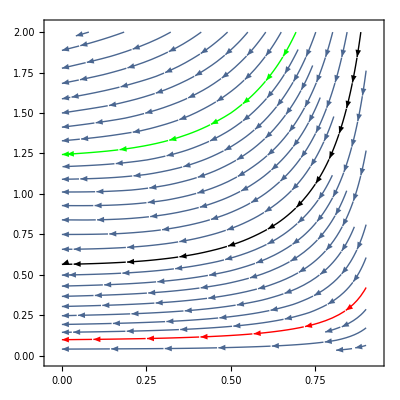

```mathematica
StreamPlot[{(-27 a^-8(1-e^2)^(-13/2)) (g4[e]+11/18 α g5[e] a^2-11/18(1+α)g6[e](1-e^2)^(1/2)a^(3/2)),(-6 a^-7(1-e^2)^(-15/2)) (g1[e]+α g2[e] a^2-(1+α)g3[e](1-e^2)^(1/2)a^(3/2))},{e,0,0.9},{a,0.01,2},StreamScale->Large,StreamPoints->{{{{0.1,0.1},Red},{{0.5,1.5},Green},{{0,αn},Black},Automatic}},Axes->True]
```

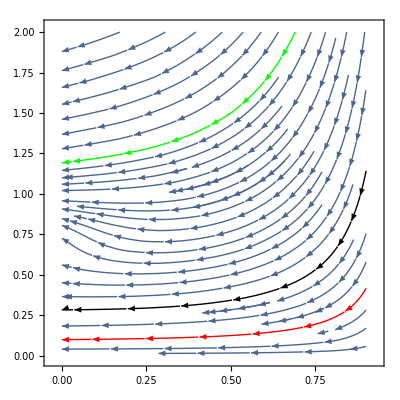

```mathematica
α = 10;
αn = α^(-2/3)(1+2/3 α^(-1/3));
StreamPlot[{(-27 a^-8(1-e^2)^(-13/2)) (g4[e]+11/18 α g5[e] a^2-11/18(1+α)g6[e](1-e^2)^(1/2)a^(3/2)),(-6 a^-7(1-e^2)^(-15/2)) (g1[e]+α g2[e] a^2-(1+α)g3[e](1-e^2)^(1/2)a^(3/2))},{e,0,0.9},{a,0.01,2},StreamScale->Large,StreamPoints->{{{{0.1,0.1},Red},{{0.5,1.5},Green},{{0,αn},Black},Automatic}},Axes->True]
```

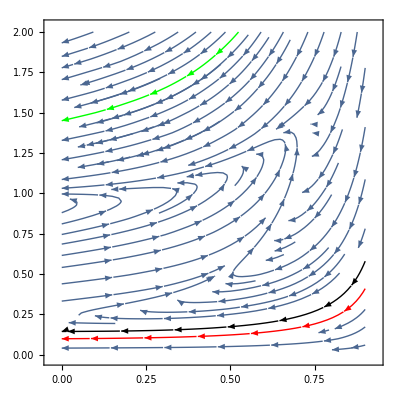

```mathematica
α = 25;
αn = α^(-2/3)(1+2/3 α^(-1/3));
StreamPlot[{(-27 a^-8(1-e^2)^(-13/2)) (g4[e]+11/18 α g5[e] a^2-11/18(1+α)g6[e](1-e^2)^(1/2)a^(3/2)),(-6 a^-7(1-e^2)^(-15/2)) (g1[e]+α g2[e] a^2-(1+α)g3[e](1-e^2)^(1/2)a^(3/2))},{e,0,0.9},{a,0.01,2},StreamScale->Large,StreamPoints->{{{{0.1,0.1},Red},{{0.1,1.5},Green},{{0,αn},Black},Automatic}},Axes->True]
```

```mathematica
Clear[α]
```

These are all consistent with Figs 5-7. But we also want to see what happens for α<4

3.5

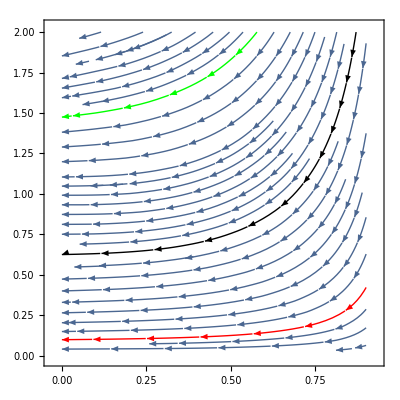

```mathematica
α = 3.5
αn = α^(-2/3)(1+2/3 α^(-1/3));
StreamPlot[{(-27 a^-8(1-e^2)^(-13/2)) (g4[e]+11/18 α g5[e] a^2-11/18(1+α)g6[e](1-e^2)^(1/2)a^(3/2)),(-6 a^-7(1-e^2)^(-15/2)) (g1[e]+α g2[e] a^2-(1+α)g3[e](1-e^2)^(1/2)a^(3/2))},{e,0,0.9},{a,0.01,2},StreamScale->Large,StreamPoints->{{{{0.1,0.1},Red},{{0.1,1.5},Green},{{0,αn},Black},Automatic}},Axes->True]
```

1

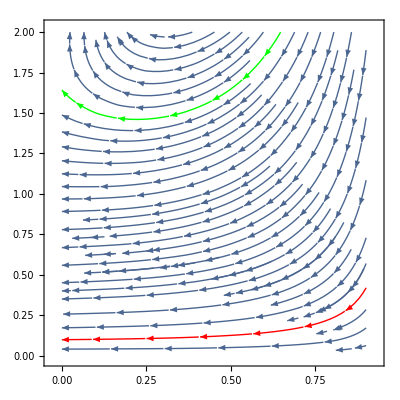

```mathematica
α = 1
αn = α^(-2/3)(1+2/3 α^(-1/3));
StreamPlot[{(-27 a^-8(1-e^2)^(-13/2)) (g4[e]+11/18 α g5[e] a^2-11/18(1+α)g6[e](1-e^2)^(1/2)a^(3/2)),(-6 a^-7(1-e^2)^(-15/2)) (g1[e]+α g2[e] a^2-(1+α)g3[e](1-e^2)^(1/2)a^(3/2))},{e,0,0.9},{a,0.01,2},StreamScale->Large,StreamPoints->{{{{0.1,0.1},Red},{{0.1,1.5},Green},{{0,αn},Black},Automatic}},Axes->True]
```

Notice there is no black line. All solutions are unstable and lead to a collision. This is consistent with the result of Hut1980.